## Cargar paquetes y definiciones

```mathematica
(* Establecer que el directorio sea el mismo que el de este notebook *)
SetDirectory[NotebookDirectory[]]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files

```mathematica
(* Cargar paquete QMB.wl *)
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

## Cálculo de superoperadores

### Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];
```

### Calculation

```mathematica
superoperators={};
```

```mathematica
AbsoluteTiming[
Do[
AppendTo[superoperators,Superoperator[t,ψ0E[[2]],eigenvalsH,eigenvecsH,L]],
{t,10^Range[-2,2,0.08]}](* tiempos equiespaciados en escala log *)
]
```

{258.768,Null}

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_2_t_log_scale.csv",Prepend[superoperators,"L=11;{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]};SeedRandom[32371];ψ0E=Table[RandomChainProductState[L-1],3];Superoperator[t,ψ0E[[2]],eigenvalsH,eigenvecsH,L];"],"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_2_t_log_scale.csv

## Phase-flip

```mathematica
(* Definir U de Stinespring para el canal phase-flip *)
MatrixForm[U={{1,-1,0,0},{0,0,1,1},{1,1,0,0},{0,0,-1,1}}/√2]
```

(1/(√2) | -1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 1/(√2)
1/(√2) | 1/(√2) | 0 | 0
0 | 0 | -1/(√2) | 1/(√2))

```mathematica
(* Calcular segundo término *)
-Table[
Conjugate[U.VectorFromKetInComputationalBasis[{i,0}]].KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].Dyad[U.VectorFromKetInComputationalBasis[{j,0}]].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]].U.VectorFromKetInComputationalBasis[{i,0}]
,{i,0,1},{j,0,1}]
```

{{-1/4,0},{0,-1/4}}

```mathematica
(* Calcular tercer término *)
Table[
Abs[Conjugate[U.VectorFromKetInComputationalBasis[{i,0}]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]].U.VectorFromKetInComputationalBasis[{j,0}]]^2
,{i,0,1},{j,0,1}]
```

{{1/4,0},{0,1/4}}

```mathematica
ConjugateTranspose[U].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]].U//MatrixForm
```

(1/2 | 1/2 | 0 | 0
-1/2 | -1/2 | 0 | 0
0 | 0 | -1/2 | 1/2
0 | 0 | -1/2 | 1/2)

```mathematica
U.VectorFromKetInComputationalBasis[{1,ψ0E}]
```

{0,1/(√2),0,-1/(√2)}

```mathematica
VectorFromKetInComputationalBasis[{0,ψ0E}].ConjugateTranspose[U]
```

{1/(√2),0,1/(√2),0}

```mathematica
MatrixPartialTrace[Dyad[,],2,2]
```

{{0,0},{0,0}}

### Investigando las tripas del segundo término

```mathematica
{i,j}={0,0};
```

```mathematica
Dyad[U.VectorFromKetInComputationalBasis[{j,0}]]//MatrixForm
```

(1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0)

```mathematica
KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].Dyad[U.VectorFromKetInComputationalBasis[{j,0}]].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]]//MatrixForm
```

(0 | 0 | 1/2 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Conjugate[U].KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].Dyad[U.VectorFromKetInComputationalBasis[{j,0}]].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]].U//MatrixForm
```

(1/4 | 1/4 | 0 | 0
0 | 0 | 0 | 0
1/4 | 1/4 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
{i,j}={1,1};
```

```mathematica
Conjugate[U].KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].Dyad[U.VectorFromKetInComputationalBasis[{j,0}]].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]].U//MatrixForm
```

(0 | 0 | -1/4 | 1/4
0 | 0 | 0 | 0
0 | 0 | 1/4 | -1/4
0 | 0 | 0 | 0)

```mathematica
{i,j}={1,0}
```

{1,0}

```mathematica
Table[Conjugate[U.VectorFromKetInComputationalBasis[{i,0}]].VectorFromKetInComputationalBasis[{0,p}],{p,0,1}]
```

{0,1/(√2)}

```mathematica
Table[VectorFromKetInComputationalBasis[{0,p}].U.VectorFromKetInComputationalBasis[{j,0}],{p,0,1}]
```

{1/(√2),0}

```mathematica
U.VectorFromKetInComputationalBasis[{1,0}]
```

{0,1/(√2),0,-1/(√2)}

```mathematica
KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].U.VectorFromKetInComputationalBasis[{0,0}]
```

{1/(√2),0,0,0}

```mathematica
(* Cálculo de ⅇ^(-ⅈ(Subscript[E, k]-Subscript[E, l])t) *) 
Table[i*Conjugate[j],{i,#},{j,#}]&[Eigenvalues[U]]
```

{{1,ⅈ,-(1+ⅈ)/(√2),(1+ⅈ)/(√2)},{-ⅈ,1,-(1-ⅈ)/(√2),(1-ⅈ)/(√2)},{-(1-ⅈ)/(√2),-(1+ⅈ)/(√2),1,-1},{(1-ⅈ)/(√2),(1+ⅈ)/(√2),-1,1}}

```mathematica
{eigenvals,eigenvecs}=Chop@Eigensystem[N@U]
```

{{0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,-1.,1.},{{0.-0.5 ⅈ,-0.5,-0.5,0.-0.5 ⅈ},{0.+0.5 ⅈ,-0.5,-0.5,0.+0.5 ⅈ},{0.270598,0.653281,-0.653281,-0.270598},{-0.653281,0.270598,-0.270598,0.653281}}}

```mathematica
{i,j}={0,0};{k,l}={1,4};
Table[
Chop[Abs[Sum[
(eigenvals[[k]]-eigenvals[[l]])*VectorFromKetInComputationalBasis[{i,0}].eigenvecs[[l]]*Conjugate[eigenvecs[[k]]].VectorFromKetInComputationalBasis[{j,0}]*Chop[Conjugate[eigenvecs[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]].eigenvecs[[k]]]+Conjugate[(eigenvals[[k]]-eigenvals[[l]])*VectorFromKetInComputationalBasis[{i,0}].eigenvecs[[l]]*Conjugate[eigenvecs[[k]]].VectorFromKetInComputationalBasis[{j,0}]*Chop[Conjugate[eigenvecs[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]].eigenvecs[[k]]]]
,{k,4},{l,4}]]^2]
,{i,0,1},{j,0,1}]
```

{{2.,2.},{0,2.}}

```mathematica
eigenvals[[1]]-eigenvals[[2]]
```

0.+1.41421 ⅈ

```mathematica
ψ0E=0
```

0

```mathematica
Table[
Chop@Abs[
Sum[
#1[[k]]Conjugate[#1[[l]]]*
Braket[#2[[k]],VectorFromKetInComputationalBasis[{j,ψ0E}]]*
Braket[VectorFromKetInComputationalBasis[{i,ψ0E}],#2[[l]]]*
Conjugate[#2[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]].#2[[k]]
&@@{eigenvals,eigenvecs}
,{k,4},{l,4}]]^2
,{i,0,1},{j,0,1}]
```

{{0.25,0},{0,0.25}}

```mathematica
{i,j}={1,1};
Table[
Chop[#1[[k]]Conjugate[#1[[l]]]*
Braket[#2[[k]],VectorFromKetInComputationalBasis[{j,ψ0E}]]*
Braket[VectorFromKetInComputationalBasis[{i,ψ0E}],#2[[l]]]*
Conjugate[#2[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]].#2[[k]]]
&@@{eigenvals,eigenvecs}
,{k,4},{l,4}]
```

{{0,-0.125,-0.0441942+0.106694 ⅈ,0.0441942+0.0183058 ⅈ},{-0.125,0,-0.0441942-0.106694 ⅈ,0.0441942-0.0183058 ⅈ},{0.0441942+0.106694 ⅈ,0.0441942-0.106694 ⅈ,-0.150888,-0.0625},{-0.0441942+0.0183058 ⅈ,-0.0441942-0.0183058 ⅈ,-0.0625,0.0258883}}

```mathematica
{i,j}={0,1};
Table[
Chop[#1[[k]]Conjugate[#1[[l]]]*
Braket[#2[[k]],VectorFromKetInComputationalBasis[{j,ψ0E}]]*
Braket[VectorFromKetInComputationalBasis[{i,ψ0E}],#2[[l]]]*
Conjugate[#2[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]].#2[[k]]]
&@@{eigenvals,eigenvecs}
,{k,4},{l,4}]//MatrixForm
```

(0 | 0.+0.125 ⅈ | 0.0183058-0.0441942 ⅈ | 0.106694+0.0441942 ⅈ
0.-0.125 ⅈ | 0 | 0.0183058+0.0441942 ⅈ | 0.106694-0.0441942 ⅈ
-0.106694+0.0441942 ⅈ | -0.106694-0.0441942 ⅈ | 0.0625 | -0.150888
-0.0183058-0.0441942 ⅈ | -0.0183058+0.0441942 ⅈ | 0.0258883 | 0.0625)

## Completamente depolarizante

```mathematica
(* Definir U de Stinespring para el canal phase-flip *)
U={{1/2,1/2,1/2,1/2,0,0,0,0},{0,0,0,0,1/2,1/2,-1/2,-1/2},{0,0,0,0,-ⅈ/2,ⅈ/2,-ⅈ/2,ⅈ/2},{1/2,-1/2,-1/2,1/2,0,0,0,0},{0,0,0,0,1/2,1/2,1/2,1/2},{1/2,1/2,-1/2,-1/2,0,0,0,0},{ⅈ/2,-ⅈ/2,ⅈ/2,-ⅈ/2,0,0,0,0},{0,0,0,0,-1/2,1/2,1/2,-1/2}}
```

{{1/2,1/2,1/2,1/2,0,0,0,0},{0,0,0,0,1/2,1/2,-1/2,-1/2},{0,0,0,0,-ⅈ/2,ⅈ/2,-ⅈ/2,ⅈ/2},{1/2,-1/2,-1/2,1/2,0,0,0,0},{0,0,0,0,1/2,1/2,1/2,1/2},{1/2,1/2,-1/2,-1/2,0,0,0,0},{ⅈ/2,-ⅈ/2,ⅈ/2,-ⅈ/2,0,0,0,0},{0,0,0,0,-1/2,1/2,1/2,-1/2}}

```mathematica
(* Calcular segundo término *)
-Table[
Conjugate[U.VectorFromKetInComputationalBasis[{i,0,0}]].KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[4]].Dyad[U.VectorFromKetInComputationalBasis[{j,0,0}]].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[4]].U.VectorFromKetInComputationalBasis[{i,0,0}]
,{i,0,1},{j,0,1}]
```

{{-1/4,0},{0,-1/4}}

```mathematica
(* Calcular tercer término *)
Table[
Abs[Conjugate[U.VectorFromKetInComputationalBasis[{i,0,0}]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[4]].U.VectorFromKetInComputationalBasis[{j,0,0}]]^2
,{i,0,1},{j,0,1}]
```

{{0,0},{0,0}}

```mathematica
(* Cálculo de ⅇ^(-ⅈ(Subscript[E, k]-Subscript[E, l])t) *) 
Table[N[i*Conjugate[j]],{i,#},{j,#}]&[Eigenvalues[U]]
```

{{1.,-1.,-1.,-1.,-0.183013+0.983111 ⅈ,-0.183013-0.983111 ⅈ,0.683013+0.730406 ⅈ,0.683013-0.730406 ⅈ},{-1.,1.,1.,1.,0.183013-0.983111 ⅈ,0.183013+0.983111 ⅈ,-0.683013-0.730406 ⅈ,-0.683013+0.730406 ⅈ},{-1.,1.,1.,1.,0.183013-0.983111 ⅈ,0.183013+0.983111 ⅈ,-0.683013-0.730406 ⅈ,-0.683013+0.730406 ⅈ},{-1.,1.,1.,1.,0.183013-0.983111 ⅈ,0.183013+0.983111 ⅈ,-0.683013-0.730406 ⅈ,-0.683013+0.730406 ⅈ},{-0.183013-0.983111 ⅈ,0.183013+0.983111 ⅈ,0.183013+0.983111 ⅈ,0.183013+0.983111 ⅈ,1.+0. ⅈ,-0.933013+0.359843 ⅈ,0.59307-0.805151 ⅈ,-0.84307-0.537803 ⅈ},{-0.183013+0.983111 ⅈ,0.183013-0.983111 ⅈ,0.183013-0.983111 ⅈ,0.183013-0.983111 ⅈ,-0.933013-0.359843 ⅈ,1.+0. ⅈ,-0.84307+0.537803 ⅈ,0.59307+0.805151 ⅈ},{0.683013-0.730406 ⅈ,-0.683013+0.730406 ⅈ,-0.683013+0.730406 ⅈ,-0.683013+0.730406 ⅈ,0.59307+0.805151 ⅈ,-0.84307-0.537803 ⅈ,1.+0. ⅈ,-0.0669873-0.997754 ⅈ},{0.683013+0.730406 ⅈ,-0.683013-0.730406 ⅈ,-0.683013-0.730406 ⅈ,-0.683013-0.730406 ⅈ,-0.84307+0.537803 ⅈ,0.59307-0.805151 ⅈ,-0.0669873+0.997754 ⅈ,1.+0. ⅈ}}

## COE

```mathematica
L=5;
```

```mathematica
U=RandomVariate[CircularOrthogonalMatrixDistribution[2^L]];
```

```mathematica
(* Calcular segundo término *)
Chop@-Table[
Conjugate[U.VectorFromKetInComputationalBasis[{i}~Join~ConstantArray[0,L-1]]].KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2^(L-1)]].Dyad[U.VectorFromKetInComputationalBasis[{i}~Join~ConstantArray[0,L-1]]].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2^(L-1)]].U.VectorFromKetInComputationalBasis[{i}~Join~ConstantArray[0,L-1]]
,{i,0,1},{j,0,1}]
```

{{-0.247817,-0.247817},{-0.249485,-0.249485}}

```mathematica
Total[,2]
```

-0.994605

```mathematica
(* Calcular tercer término *)
Chop@Table[
Abs[Conjugate[U.VectorFromKetInComputationalBasis[{i}~Join~ConstantArray[0,L-1]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2^(L-1)]].U.VectorFromKetInComputationalBasis[{i}~Join~ConstantArray[0,L-1]]]^2
,{i,0,1},{j,0,1}]
```

{{0.000317217,0.000317217},{0.00348579,0.00348579}}

```mathematica
Total[,2]
```

0.00760602

```mathematica
(1++)
```

0.0130012

```mathematica
L=8;Module[{H},
H=H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
U=MatrixExp[-I H];
{eigenvals,eigenvecs}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
Purity[Reshuffle[Superoperator[10,VectorFromKetInComputationalBasis[ConstantArray[0,L-1]],eigenvals,eigenvecs,L]]/2]
```

0.255871+0. ⅈ

## Pureza con Hamiltoniano GOE

```mathematica
L=10;
```

```mathematica
(* Calcular un Hamiltoniano de GOE y obtener sus eigenvalores y eigenvectores *)
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
(*U=MatrixExp[-I H];*)
{eigenvalsH,eigenvecsH}=Chop[Eigensystem[H]];
]
```

```mathematica
(* Revisar que los eigenvectores esten normalizados *)
AllTrue[Norm/@eigenvecsH,#==1.&]
```

True

```mathematica
(* Definir un estado inicial para el entorno de L-1 espines *)
(*ψ0E=VectorFromKetInComputationalBasis[{0,0,0,0}];*)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular la pureza de la matriz de Choi con eq:choi:chaometer:purity:1 *)
choiPurityGOE=Table[
{t,
1/4*Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]
]^2
,{i,2},{j,2},{p,2},{q,2}]}
,{t,10^Range[-2,2,0.08]}];
```

```mathematica
choiPurityGOE//Dimensions
```

{51,2}

```mathematica
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
```

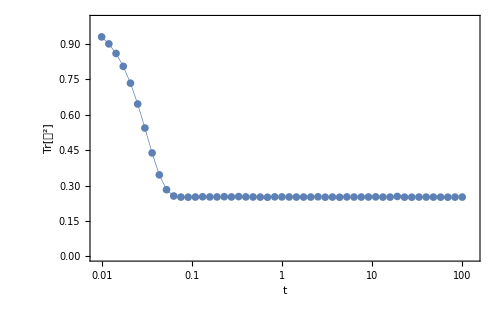

```mathematica
ListLogLinearPlot[choiPurityGOE,
PlotRange->{{10^(-2)-0.001,100+30},{0,1}},
Joined->True,
PlotMarkers->{Automatic,6},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

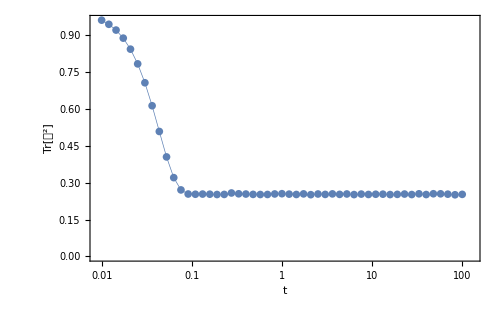

```mathematica
ListLogLinearPlot[choiPurityGOE,
PlotRange->{{10^-2-0.001,100+30},Automatic},
Joined->True,
PlotMarkers->{Automatic,6},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

```mathematica
ListLogLinearPlot[choiPurityGOE,
PlotRange->{{10^-2-0.001,100+30},Automatic},
Joined->True,
PlotMarkers->{Automatic,6},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

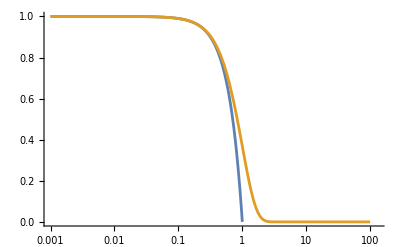

```mathematica
LogLinearPlot[{1-t^2,Exp[-t^2]},
{t,10^(-3),100},
PlotRange->{{10^(-3)-0.001,100+30},{0,1}}]
```

## Pureza de canal del caómetro, caótico

```mathematica
AbsoluteTiming[
choiChaoticPurity=Chop[Map[Purity[1/2.Reshuffle[#]]&,superoperators]];
]
```

{0.007134,Null}

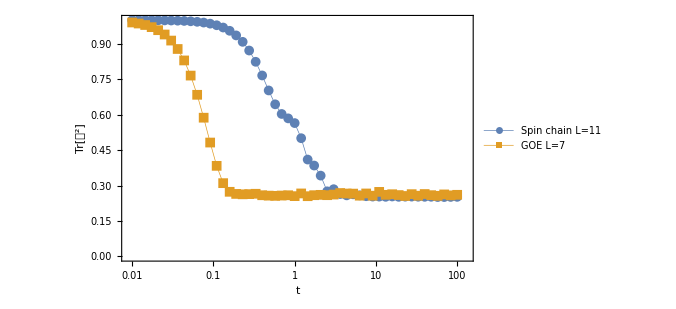

```mathematica
ListLogLinearPlot[{Transpose[{10^Range[-2,2,0.08],choiChaoticPurity}],%185},
PlotRange->{{10^-2-0.001,100+30},Automatic},
PlotLegends->Placed[LineLegend[{"Spin chain "<>ToString[TraditionalForm[HoldForm[L=11]]],"GOE "<>ToString[TraditionalForm[HoldForm[L=7]]]},LegendMarkerSize->{{30,20}}],{Right,Top}],
Joined->True,
PlotMarkers->{Automatic,10},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

```mathematica
1-2t^2/.{t->0.091}
```

0.983438

```mathematica
1-1.2t^2/.{t->0.83}
```

0.17332

```mathematica
1/1.2
```

0.833333

```mathematica
Exp[-0.5t^2]/.{t->2.51}
```

0.04285

```mathematica
0.5^-1*Log[4]
```

2.77259

```mathematica
AbsoluteTiming[
choiChaoticPurity=Chop[Map[Purity[1/2.Reshuffle[#]]&,superoperators]];
]
```

{0.00291,Null}

```mathematica
ArrayReshape[choiChaoticPurity,{2,51}]//Dimensions
```

{2,51}

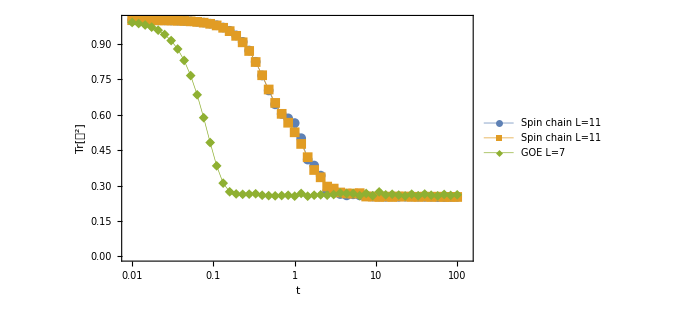

```mathematica
ListLogLinearPlot[Join[Transpose[{10^Range[-2,2,0.08],#}]&/@ArrayReshape[choiChaoticPurity,{2,51}],{%185}],
PlotRange->{{10^-2-0.001,100+30},Automatic},
PlotLegends->Placed[LineLegend[{"Spin chain "<>ToString[TraditionalForm[HoldForm[L=11]]],"Spin chain "<>ToString[TraditionalForm[HoldForm[L=11]]],"GOE "<>ToString[TraditionalForm[HoldForm[L=7]]]},LegendMarkerSize->{{30,20}},
LabelStyle->Directive[FontFamily->"Arial",FontSize->18]],{Right,Top}],
Joined->True,
PlotMarkers->{Automatic,10},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

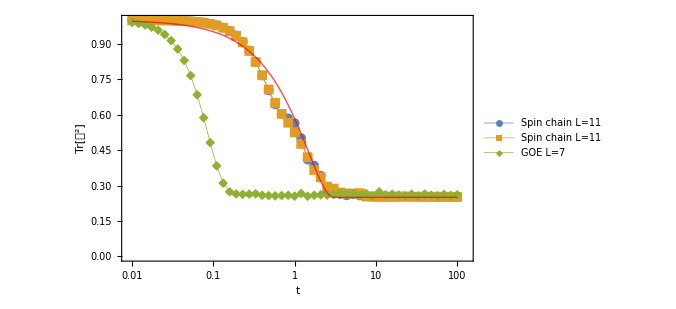

```mathematica
Show[,LogLinearPlot[If[t<=3,Purity[1/2*Reshuffle[QubitChannelSuperoperator[Table[1-t/3,3],{0,0,0}]]],0.25],{t,10^-2,100},PlotStyle->Directive[Red,Thick,Opacity[0.7]]]]
```

```mathematica
If[p<=1,Purity[1/2*Reshuffle[QubitChannelSuperoperator[Table[1-t/3,3],{0,0,0}]]],0.25]
```

If[p≤1,Purity[1/2 Reshuffle[QubitChannelSuperoperator[Table[1-t/3,3],{0,0,0}]]],0.25]

```mathematica
10^(1-0.01)/10
```

0.977237

```mathematica
1-0.01
```

0.99